# SVM-BDS-BDT Comparison Results, 7/15/16

## Raw Data

## SVM: c, γ, Number of Support Vectors, False Positive Fraction, False Negative Fraction, Efficiency, Distance, Time

```mathematica
SVMLinearHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearHardTestingAll0715"}],"Table"];
SVMLinearHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearHardTestingSignal0715"}],"Table"];
SVMLinearHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearHardTestingBackground0715"}],"Table"];

SVMLinearSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearSoftTestingAll0715"}],"Table"];
SVMLinearSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearSoftTestingSignal0715"}],"Table"];
SVMLinearSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearSoftTestingBackground0715"}],"Table"];


SVMCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleHardTestingAll0715"}],"Table"];
SVMCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleHardTestingSignal0715"}],"Table"];
SVMCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleHardTestingBackground0715"}],"Table"];

SVMCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleSoftTestingAll0715"}],"Table"];
SVMCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleSoftTestingSignal0715"}],"Table"];
SVMCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleSoftTestingBackground0715"}],"Table"];


SVMTwoCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleHardTestingAll0715"}],"Table"];
SVMTwoCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleHardTestingSignal0715"}],"Table"];
SVMTwoCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleHardTestingBackground0715"}],"Table"];

SVMTwoCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleSoftTestingAll0715"}],"Table"];
SVMTwoCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleSoftTestingSignal0715"}],"Table"];
SVMTwoCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleSoftTestingBackground0715"}],"Table"];


SVMAllRawData = {SVMLinearHardTestingAllRawData,SVMLinearHardTestingSignalRawData,SVMLinearHardTestingBackgroundRawData,SVMLinearSoftTestingAllRawData,SVMLinearSoftTestingSignalRawData,SVMLinearSoftTestingBackgroundRawData,SVMCircleHardTestingAllRawData,SVMCircleHardTestingSignalRawData,SVMCircleHardTestingBackgroundRawData,SVMCircleSoftTestingAllRawData,SVMCircleSoftTestingSignalRawData,SVMCircleSoftTestingBackgroundRawData,SVMTwoCircleHardTestingAllRawData,SVMTwoCircleHardTestingSignalRawData,SVMTwoCircleHardTestingBackgroundRawData,SVMTwoCircleSoftTestingAllRawData,SVMTwoCircleSoftTestingSignalRawData,SVMTwoCircleSoftTestingBackgroundRawData};

SVMAllDataTypes={"Linear Hard Testing All","Linear Hard Testing Signal","Linear Hard Testing Background","Linear Soft Testing All","Linear Soft Testing Signal","Linear Soft Testing Background","Circle Hard Testing All","Circle Hard Testing Signal","Circle Hard Testing Background","Circle Soft Testing All","Circle Soft Testing Signal","Circle Soft Testing Background","Two Circle Hard Testing All","Two Circle Hard Testing Signal","Two Circle Hard Testing Background","Two Circle Soft Testing All","Two Circle Soft Testing Signal","Two Circle Soft Testing Background"};
```

## BDS: Number of Stumps, Efficiency, False Positive Fraction, False Negative Fraction, Distance, Time

```mathematica
BDSLinearHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearHardTestingAll0715"}],"Table"];
BDSLinearHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearHardTestingSignal0715"}],"Table"];
BDSLinearHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearHardTestingBackground0715"}],"Table"];

BDSLinearSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearSoftTestingAll0715"}],"Table"];
BDSLinearSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearSoftTestingSignal0715"}],"Table"];
BDSLinearSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearSoftTestingBackground0715"}],"Table"];


BDSCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleHardTestingAll0715"}],"Table"];
BDSCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleHardTestingSignal0715"}],"Table"];
BDSCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleHardTestingBackground0715"}],"Table"];

BDSCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleSoftTestingAll0715"}],"Table"];
BDSCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleSoftTestingSignal0715"}],"Table"];
BDSCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleSoftTestingBackground0715"}],"Table"];


BDSTwoCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleHardTestingAll0715"}],"Table"];
BDSTwoCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleHardTestingSignal0715"}],"Table"];
BDSTwoCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleHardTestingBackground0715"}],"Table"];

BDSTwoCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleSoftTestingAll0715"}],"Table"];
BDSTwoCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleSoftTestingSignal0715"}],"Table"];
BDSTwoCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleSoftTestingBackground0715"}],"Table"];


BDSAllRawData={BDSLinearHardTestingAllRawData,BDSLinearHardTestingSignalRawData,BDSLinearHardTestingBackgroundRawData,BDSLinearSoftTestingAllRawData,BDSLinearSoftTestingSignalRawData,BDSLinearSoftTestingBackgroundRawData,BDSCircleHardTestingAllRawData,BDSCircleHardTestingSignalRawData,BDSCircleHardTestingBackgroundRawData,BDSCircleSoftTestingAllRawData,BDSCircleSoftTestingSignalRawData,BDSCircleSoftTestingBackgroundRawData,BDSTwoCircleHardTestingAllRawData,BDSTwoCircleHardTestingSignalRawData,BDSTwoCircleHardTestingBackgroundRawData,BDSTwoCircleSoftTestingAllRawData,BDSTwoCircleSoftTestingSignalRawData,BDSTwoCircleSoftTestingBackgroundRawData};

BDSAllDataTypes={"Linear Hard Testing All","Linear Hard Testing Signal","Linear Hard Testing Background","Linear Soft Testing All","Linear Soft Testing Signal","Linear Soft Testing Background","Circle Hard Testing All","Circle Hard Testing Signal","Circle Hard Testing Background","Circle Soft Testing All","Circle Soft Testing Signal","Circle Soft Testing Background","Two Circle Hard Testing All","Two Circle Hard Testing Signal","Two Circle Hard Testing Background","Two Circle Soft Testing All","Two Circle Soft Testing Signal","Two Circle Soft Testing Background"};
```

## BDT: Number of Trees, Efficiency, False Positive Fraction, False Negative Fraction, Distance, Time

```mathematica
BDTLinearHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearHardTestingAll0715"}],"Table"];
BDTLinearHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearHardTestingSignal0715"}],"Table"];
BDTLinearHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearHardTestingBackground0715"}],"Table"];

BDTLinearSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearSoftTestingAll0715"}],"Table"];
BDTLinearSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearSoftTestingSignal0715"}],"Table"];
BDTLinearSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearSoftTestingBackground0715"}],"Table"];


BDTCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleHardTestingAll0715"}],"Table"];
BDTCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleHardTestingSignal0715"}],"Table"];
BDTCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleHardTestingBackground0715"}],"Table"];

BDTCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleSoftTestingAll0715"}],"Table"];
BDTCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleSoftTestingSignal0715"}],"Table"];
BDTCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleSoftTestingBackground0715"}],"Table"];


BDTTwoCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleHardTestingAll0715"}],"Table"];
BDTTwoCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleHardTestingSignal0715"}],"Table"];
BDTTwoCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleHardTestingBackground0715"}],"Table"];

BDTTwoCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleSoftTestingAll0715"}],"Table"];
BDTTwoCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleSoftTestingSignal0715"}],"Table"];
BDTTwoCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleSoftTestingBackground0715"}],"Table"];


BDTAllRawData={BDTLinearHardTestingAllRawData,BDTLinearHardTestingSignalRawData,BDTLinearHardTestingBackgroundRawData,BDTLinearSoftTestingAllRawData,BDTLinearSoftTestingSignalRawData,BDTLinearSoftTestingBackgroundRawData,BDTCircleHardTestingAllRawData,BDTCircleHardTestingSignalRawData,BDTCircleHardTestingBackgroundRawData,BDTCircleSoftTestingAllRawData,BDTCircleSoftTestingSignalRawData,BDTCircleSoftTestingBackgroundRawData,BDTTwoCircleHardTestingAllRawData,BDTTwoCircleHardTestingSignalRawData,BDTTwoCircleHardTestingBackgroundRawData,BDTTwoCircleSoftTestingAllRawData,BDTTwoCircleSoftTestingSignalRawData,BDTTwoCircleSoftTestingBackgroundRawData};

BDTAllDataTypes={"Linear Hard Testing All","Linear Hard Testing Signal","Linear Hard Testing Background","Linear Soft Testing All","Linear Soft Testing Signal","Linear Soft Testing Background","Circle Hard Testing All","Circle Hard Testing Signal","Circle Hard Testing Background","Circle Soft Testing All","Circle Soft Testing Signal","Circle Soft Testing Background","Two Circle Hard Testing All","Two Circle Hard Testing Signal","Two Circle Hard Testing Background","Two Circle Soft Testing All","Two Circle Soft Testing Signal","Two Circle Soft Testing Background"};
```

## Formatted Datasets

## SVM

### c-γ-Efficiency

```mathematica
SVMCGE[RawData_]:=RawData[[All,{1,2, 6}]]
```

### Log(c)-γ-Efficiency

```mathematica
SVMLogCGE[RawData_]:=MapAt[Log10, RawData[[All,{1,2, 6}]], {All, 1}]
```

### c-γ-Distance

```mathematica
SVMCGD[RawData_]:=RawData[[All,{1,2, 7}]]
```

### Log(c)-γ-Distance

```mathematica
SVMLogCGD[RawData_]:=MapAt[Log10, RawData[[All,{1,2, 7}]], {All, 1}]
```

### False Positive Fraction-Efficiency

```mathematica
SVMFPE[RawData_]:= RawData[[All,{4,6}]]
```

## BDS

### Number of Stumps-Efficiency

```mathematica
BDSSE[RawData_]:=RawData[[All,{1,2}]]
```

### Number of Stumps-Distance

```mathematica
BDSSD[RawData_]:=RawData[[All,{1,5}]]
```

### False Positive Fraction-Efficiency

```mathematica
BDSFPE[RawData_]:= RawData[[All,{3,2}]]
```

## BDT

### Number of Trees-Efficiency

```mathematica
BDTTE[RawData_]:=RawData[[All,{1,2}]]
```

### Number of Trees-Distance

```mathematica
BDTTD[RawData_]:=RawData[[All,{1,5}]]
```

### False Positive Fraction-Efficiency

```mathematica
BDTFPE[RawData_]:= RawData[[All,{3,2}]]
```

## Optimizing Parameters

## SVM

### Overall

```mathematica
SVMBest[RawData_]:=First[SortBy[RawData[[All,{8,1,2,6,5,7}]],Last]];
```

```mathematica
SVMBestResultTable=Grid[{{"Data Set","Runtime (s)","c","γ","Efficiency","False Negative Fraction","Distance"},Prepend[SVMBest[SVMLinearHardTestingAllRawData],"Linear Hard Testing All"],Prepend[SVMBest[SVMLinearHardTestingSignalRawData],"Linear Hard Testing Signal"],Prepend[SVMBest[SVMLinearHardTestingBackgroundRawData],"Linear Hard Testing Background"],Prepend[SVMBest[SVMLinearSoftTestingAllRawData],"Linear Soft Testing All"],Prepend[SVMBest[SVMLinearSoftTestingSignalRawData],"Linear Soft Testing Signal"],Prepend[SVMBest[SVMLinearSoftTestingBackgroundRawData],"Linear Soft Testing Background"],Prepend[SVMBest[SVMCircleHardTestingAllRawData],"Circle Hard Testing All"],Prepend[SVMBest[SVMCircleHardTestingSignalRawData],"Circle Hard Testing Signal"],Prepend[SVMBest[SVMCircleHardTestingBackgroundRawData],"Circle Hard Testing Background"],Prepend[SVMBest[SVMCircleSoftTestingAllRawData],"Circle Soft Testing All"],Prepend[SVMBest[SVMCircleSoftTestingSignalRawData],"Circle Soft Testing Signal"],Prepend[SVMBest[SVMCircleSoftTestingBackgroundRawData],"Circle Soft Testing Background"],Prepend[SVMBest[SVMTwoCircleHardTestingAllRawData],"Two Circle Hard Testing All"],Prepend[SVMBest[SVMTwoCircleHardTestingSignalRawData],"Two Circle Hard Testing Signal"],Prepend[SVMBest[SVMTwoCircleHardTestingBackgroundRawData],"Two Circle Hard Testing Background"],Prepend[SVMBest[SVMTwoCircleSoftTestingAllRawData],"Two Circle Soft Testing All"],Prepend[SVMBest[SVMTwoCircleSoftTestingSignalRawData],"Two Circle Soft Testing Signal"],Prepend[SVMBest[SVMTwoCircleSoftTestingBackgroundRawData],"Two Circle Soft Testing Background"]},Frame->All];
```

### Fast Runtime

```mathematica
SVMOneDayBest[RawData_]:=First[SortBy[Select[RawData[[All,{8,1,2,6,5,7}]],#⟦1⟧≤ 374&],Last]];
```

```mathematica
SVMOneDayBestResultTable=Grid[{{"Data Set","Runtime (s)","c","γ","Efficiency","False Negative Fraction","Distance"},Prepend[SVMOneDayBest[SVMLinearHardTestingAllRawData],"Linear Hard Testing All"],Prepend[SVMOneDayBest[SVMLinearHardTestingSignalRawData],"Linear Hard Testing Signal"],Prepend[SVMOneDayBest[SVMLinearHardTestingBackgroundRawData],"Linear Hard Testing Background"],Prepend[SVMOneDayBest[SVMLinearSoftTestingAllRawData],"Linear Soft Testing All"],Prepend[SVMOneDayBest[SVMLinearSoftTestingSignalRawData],"Linear Soft Testing Signal"],Prepend[SVMOneDayBest[SVMLinearSoftTestingBackgroundRawData],"Linear Soft Testing Background"],Prepend[SVMOneDayBest[SVMCircleHardTestingAllRawData],"Circle Hard Testing All"],Prepend[SVMOneDayBest[SVMCircleHardTestingSignalRawData],"Circle Hard Testing Signal"],Prepend[SVMOneDayBest[SVMCircleHardTestingBackgroundRawData],"Circle Hard Testing Background"],Prepend[SVMOneDayBest[SVMCircleSoftTestingAllRawData],"Circle Soft Testing All"],Prepend[SVMOneDayBest[SVMCircleSoftTestingSignalRawData],"Circle Soft Testing Signal"],Prepend[SVMOneDayBest[SVMCircleSoftTestingBackgroundRawData],"Circle Soft Testing Background"],Prepend[SVMOneDayBest[SVMTwoCircleHardTestingAllRawData],"Two Circle Hard Testing All"],Prepend[SVMOneDayBest[SVMTwoCircleHardTestingSignalRawData],"Two Circle Hard Testing Signal"],Prepend[SVMOneDayBest[SVMTwoCircleHardTestingBackgroundRawData],"Two Circle Hard Testing Background"],Prepend[SVMOneDayBest[SVMTwoCircleSoftTestingAllRawData],"Two Circle Soft Testing All"],Prepend[SVMOneDayBest[SVMTwoCircleSoftTestingSignalRawData],"Two Circle Soft Testing Signal"],Prepend[SVMOneDayBest[SVMTwoCircleSoftTestingBackgroundRawData],"Two Circle Soft Testing Background"]},Frame->All];
```

## BDS

### Overall

```mathematica
BDSBest[RawData_]:=First[SortBy[RawData[[All,{6,1,2,4,5}]],Last]];
```

```mathematica
BDSBestResultTable=Grid[{{"Data Set","Runtime (s)","Number of Trees","Efficiency","False Negative Fraction","Distance"},Prepend[BDSBest[BDSLinearHardTestingAllRawData],"Linear Hard Testing All"],Prepend[BDSBest[BDSLinearHardTestingSignalRawData],"Linear Hard Testing Signal"],Prepend[BDSBest[BDSLinearHardTestingBackgroundRawData],"Linear Hard Testing Background"],Prepend[BDSBest[BDSLinearSoftTestingAllRawData],"Linear Soft Testing All"],Prepend[BDSBest[BDSLinearSoftTestingSignalRawData],"Linear Soft Testing Signal"],Prepend[BDSBest[BDSLinearSoftTestingBackgroundRawData],"Linear Soft Testing Background"],Prepend[BDSBest[BDSCircleHardTestingAllRawData],"Circle Hard Testing All"],Prepend[BDSBest[BDSCircleHardTestingSignalRawData],"Circle Hard Testing Signal"],Prepend[BDSBest[BDSCircleHardTestingBackgroundRawData],"Circle Hard Testing Background"],Prepend[BDSBest[BDSCircleSoftTestingAllRawData],"Circle Soft Testing All"],Prepend[BDSBest[BDSCircleSoftTestingSignalRawData],"Circle Soft Testing Signal"],Prepend[BDSBest[BDSCircleSoftTestingBackgroundRawData],"Circle Soft Testing Background"],Prepend[BDSBest[BDSTwoCircleHardTestingAllRawData],"Two Circle Hard Testing All"],Prepend[BDSBest[BDSTwoCircleHardTestingSignalRawData],"Two Circle Hard Testing Signal"],Prepend[BDSBest[BDSTwoCircleHardTestingBackgroundRawData],"Two Circle Hard Testing Background"],Prepend[BDSBest[BDSTwoCircleSoftTestingAllRawData],"Two Circle Soft Testing All"],Prepend[BDSBest[BDSTwoCircleSoftTestingSignalRawData],"Two Circle Soft Testing Signal"],Prepend[BDSBest[BDSTwoCircleSoftTestingBackgroundRawData],"Two Circle Soft Testing Background"]},Frame->All];
```

### Fast Runtime

```mathematica
BDSOneDayBest[RawData_]:=First[SortBy[Select[RawData[[All,{6,1,2,4,5}]],#⟦1⟧≤ 374&],Last]];
```

```mathematica
BDSOneDayBestResultTable=Grid[{{"Data Set","Runtime (s)","Number of Trees","Efficiency","False Negative Fraction","Distance"},Prepend[BDSOneDayBest[BDSLinearHardTestingAllRawData],"Linear Hard Testing All"],Prepend[BDSOneDayBest[BDSLinearHardTestingSignalRawData],"Linear Hard Testing Signal"],Prepend[BDSOneDayBest[BDSLinearHardTestingBackgroundRawData],"Linear Hard Testing Background"],Prepend[BDSOneDayBest[BDSLinearSoftTestingAllRawData],"Linear Soft Testing All"],Prepend[BDSOneDayBest[BDSLinearSoftTestingSignalRawData],"Linear Soft Testing Signal"],Prepend[BDSOneDayBest[BDSLinearSoftTestingBackgroundRawData],"Linear Soft Testing Background"],Prepend[BDSOneDayBest[BDSCircleHardTestingAllRawData],"Circle Hard Testing All"],Prepend[BDSOneDayBest[BDSCircleHardTestingSignalRawData],"Circle Hard Testing Signal"],Prepend[BDSOneDayBest[BDSCircleHardTestingBackgroundRawData],"Circle Hard Testing Background"],Prepend[BDSOneDayBest[BDSCircleSoftTestingAllRawData],"Circle Soft Testing All"],Prepend[BDSOneDayBest[BDSCircleSoftTestingSignalRawData],"Circle Soft Testing Signal"],Prepend[BDSOneDayBest[BDSCircleSoftTestingBackgroundRawData],"Circle Soft Testing Background"],Prepend[BDSOneDayBest[BDSTwoCircleHardTestingAllRawData],"Two Circle Hard Testing All"],Prepend[BDSOneDayBest[BDSTwoCircleHardTestingSignalRawData],"Two Circle Hard Testing Signal"],Prepend[BDSOneDayBest[BDSTwoCircleHardTestingBackgroundRawData],"Two Circle Hard Testing Background"],Prepend[BDSOneDayBest[BDSTwoCircleSoftTestingAllRawData],"Two Circle Soft Testing All"],Prepend[BDSOneDayBest[BDSTwoCircleSoftTestingSignalRawData],"Two Circle Soft Testing Signal"],Prepend[BDSOneDayBest[BDSTwoCircleSoftTestingBackgroundRawData],"Two Circle Soft Testing Background"]},Frame->All];
```

## BDT

### Overall

```mathematica
BDTBest[RawData_]:=First[SortBy[RawData[[All,{6,1,2,4,5}]],Last]];
```

```mathematica
BDTBestResultTable=Grid[{{"Data Set","Runtime (s)","Number of Trees","Efficiency","False Negative Fraction","Distance"},Prepend[BDTBest[BDTLinearHardTestingAllRawData],"Linear Hard Testing All"],Prepend[BDTBest[BDTLinearHardTestingSignalRawData],"Linear Hard Testing Signal"],Prepend[BDTBest[BDTLinearHardTestingBackgroundRawData],"Linear Hard Testing Background"],Prepend[BDTBest[BDTLinearSoftTestingAllRawData],"Linear Soft Testing All"],Prepend[BDTBest[BDTLinearSoftTestingSignalRawData],"Linear Soft Testing Signal"],Prepend[BDTBest[BDTLinearSoftTestingBackgroundRawData],"Linear Soft Testing Background"],Prepend[BDTBest[BDTCircleHardTestingAllRawData],"Circle Hard Testing All"],Prepend[BDTBest[BDTCircleHardTestingSignalRawData],"Circle Hard Testing Signal"],Prepend[BDTBest[BDTCircleHardTestingBackgroundRawData],"Circle Hard Testing Background"],Prepend[BDTBest[BDTCircleSoftTestingAllRawData],"Circle Soft Testing All"],Prepend[BDTBest[BDTCircleSoftTestingSignalRawData],"Circle Soft Testing Signal"],Prepend[BDTBest[BDTCircleSoftTestingBackgroundRawData],"Circle Soft Testing Background"],Prepend[BDTBest[BDTTwoCircleHardTestingAllRawData],"Two Circle Hard Testing All"],Prepend[BDTBest[BDTTwoCircleHardTestingSignalRawData],"Two Circle Hard Testing Signal"],Prepend[BDTBest[BDTTwoCircleHardTestingBackgroundRawData],"Two Circle Hard Testing Background"],Prepend[BDTBest[BDTTwoCircleSoftTestingAllRawData],"Two Circle Soft Testing All"],Prepend[BDTBest[BDTTwoCircleSoftTestingSignalRawData],"Two Circle Soft Testing Signal"],Prepend[BDTBest[BDTTwoCircleSoftTestingBackgroundRawData],"Two Circle Soft Testing Background"]},Frame->All];
```

### Fast Runtime

```mathematica
BDTOneDayBest[RawData_]:=First[SortBy[Select[RawData[[All,{6,1,2,4,5}]],#⟦1⟧≤ 374&],Last]];
```

```mathematica
BDTOneDayBestResultTable=Grid[{{"Data Set","Runtime (s)","Number of Trees","Efficiency","False Negative Fraction","Distance"},Prepend[BDTOneDayBest[BDTLinearHardTestingAllRawData],"Linear Hard Testing All"],Prepend[BDTOneDayBest[BDTLinearHardTestingSignalRawData],"Linear Hard Testing Signal"],Prepend[BDTOneDayBest[BDTLinearHardTestingBackgroundRawData],"Linear Hard Testing Background"],Prepend[BDTOneDayBest[BDTLinearSoftTestingAllRawData],"Linear Soft Testing All"],Prepend[BDTOneDayBest[BDTLinearSoftTestingSignalRawData],"Linear Soft Testing Signal"],Prepend[BDTOneDayBest[BDTLinearSoftTestingBackgroundRawData],"Linear Soft Testing Background"],Prepend[BDTOneDayBest[BDTCircleHardTestingAllRawData],"Circle Hard Testing All"],Prepend[BDTOneDayBest[BDTCircleHardTestingSignalRawData],"Circle Hard Testing Signal"],Prepend[BDTOneDayBest[BDTCircleHardTestingBackgroundRawData],"Circle Hard Testing Background"],Prepend[BDTOneDayBest[BDTCircleSoftTestingAllRawData],"Circle Soft Testing All"],Prepend[BDTOneDayBest[BDTCircleSoftTestingSignalRawData],"Circle Soft Testing Signal"],Prepend[BDTOneDayBest[BDTCircleSoftTestingBackgroundRawData],"Circle Soft Testing Background"],Prepend[BDTOneDayBest[BDTTwoCircleHardTestingAllRawData],"Two Circle Hard Testing All"],Prepend[BDTOneDayBest[BDTTwoCircleHardTestingSignalRawData],"Two Circle Hard Testing Signal"],Prepend[BDTOneDayBest[BDTTwoCircleHardTestingBackgroundRawData],"Two Circle Hard Testing Background"],Prepend[BDTOneDayBest[BDTTwoCircleSoftTestingAllRawData],"Two Circle Soft Testing All"],Prepend[BDTOneDayBest[BDTTwoCircleSoftTestingSignalRawData],"Two Circle Soft Testing Signal"],Prepend[BDTOneDayBest[BDTTwoCircleSoftTestingBackgroundRawData],"Two Circle Soft Testing Background"]},Frame->All];
```

## Developing Plots

## SVM

### c-γ-Efficiency

```mathematica
SVMCGEPlot[RawData_,DataType_]:=ListPlot3D[SVMCGE[RawData], AxesLabel->{c, γ, Efficiency}, PlotLabel->StringJoin["SVM ",DataType," c-γ-Efficiency"],PlotStyle->Green]
```

### Log(c)-γ-Efficiency

```mathematica
SVMLogCGEPlot[RawData_,DataType_]:=ListPlot3D[SVMLogCGE[RawData], AxesLabel->{c, γ, Efficiency}, PlotLabel->StringJoin["SVM ",DataType," Log(c)-γ-Efficiency"],PlotStyle->Green]
```

### c-γ-Distance

```mathematica
SVMCGDPlot[RawData_,DataType_]:=ListPlot3D[SVMCGD[RawData], AxesLabel->{c, γ, Distance}, PlotLabel->StringJoin["SVM ",DataType," c-γ-Distance"],PlotStyle->Green]
```

### Log(c)-γ-Distance

```mathematica
SVMLogCGDPlot[RawData_,DataType_]:=ListPlot3D[SVMLogCGD[RawData], AxesLabel->{c, γ, Distance}, PlotLabel->StringJoin["SVM ",DataType," Log(c)-γ-Distance"],PlotStyle->Green]
```

### Efficiency-1 - False Positive Fraction

```mathematica
SVMEFPPlot[RawData_,DataType_]:=ListPlot[SVMEFP[RawData], AxesLabel->{Efficiency,"1 - False Positive Fraction"}, PlotLabel->StringJoin["SVM ",DataType," Efficiency-1 - False Positive Fraction"],PlotStyle->Darker[Green]]
```

### Efficiency-1 - False Negative Fraction

```mathematica
SVMEFNPlot[RawData_,DataType_]:=ListPlot[SVMEFN[RawData], AxesLabel->{Efficiency,"1 - False Negative Fraction"}, PlotLabel->StringJoin["SVM ",DataType," Efficiency-1 - False Negative Fraction"],PlotStyle->Darker[Green]]
```

### False Positive Fraction-Efficiency

```mathematica
SVMFPEPlot[RawData_,DataType_]:=ListPlot[SVMFPE[RawData], AxesLabel->{"False Positive Fraction",Efficiency}, PlotLabel->StringJoin["SVM ",DataType," False Positive Fraction-Efficiency"],PlotStyle->Darker[Green]]
```

## BDS

### Number of Stumps-Efficiency

```mathematica
BDSSEPlot[RawData_,DataType_]:=ListPlot[BDSSE[RawData],AxesLabel->{"Number of Stumps",Efficiency},PlotLabel->StringJoin["BDS ",DataType," Number of Stumps-Efficiency"],PlotStyle->Red]
```

### Number of Stumps-Distance

```mathematica
BDSSDPlot[RawData_,DataType_]:=ListPlot[BDSSD[RawData],AxesLabel->{"Number of Stumps",Distance},PlotLabel->StringJoin["BDS ",DataType," Number of Stumps-Distance"],PlotStyle->Red]
```

### Efficiency-1 - False Positive Fraction

```mathematica
BDSEFPPlot[RawData_,DataType_]:=ListPlot[BDSEFN[RawData],AxesLabel->{Efficiency,"1 - False Positive Fraction"},PlotLabel->StringJoin["BDS ",DataType," Efficiency-1 - False Positive Fraction"],PlotStyle->Red]
```

### Efficiency-1 - False Negative Fraction

```mathematica
BDSEFNPlot[RawData_,DataType_]:=ListPlot[BDSEFN[RawData],AxesLabel->{Efficiency,"1 - False Negative Fraction"},PlotLabel->StringJoin["BDS ",DataType," Efficiency-1 - False Negative Fraction"],PlotStyle->Red]
```

### False Positive Fraction-Efficiency

```mathematica
BDSFPEPlot[RawData_,DataType_]:=ListPlot[BDSFPE[RawData],AxesLabel->{"False Positive Fraction",Efficiency},PlotLabel->StringJoin["BDS ",DataType," False Positive Fraction-Efficiency"],PlotStyle->Red]
```

## BDT

### Number of Trees-Efficiency

```mathematica
BDTTEPlot[RawData_,DataType_]:=ListPlot[BDTTE[RawData],AxesLabel->{"Number of Trees",Efficiency},PlotLabel->StringJoin["BDT ",DataType," Number of Trees-Efficiency"],PlotStyle->Blue]
```

### Number of Trees-Distance

```mathematica
BDTTDPlot[RawData_,DataType_]:=ListPlot[BDTTD[RawData],AxesLabel->{"Number of Trees",Distance},PlotLabel->StringJoin["BDT ",DataType," Number of Trees-Distance"],PlotStyle->Blue]
```

### Efficiency-1 - False Positive Fraction

```mathematica
BDTEFPPlot[RawData_,DataType_]:=ListPlot[BDTEFN[RawData],AxesLabel->{Efficiency,"1 - False Positive Fraction"},PlotLabel->StringJoin["BDT ",DataType," Efficiency-1 - False Positive Fraction"],PlotStyle->Blue]
```

### Efficiency-1 - False Negative Fraction

```mathematica
BDTEFNPlot[RawData_,DataType_]:=ListPlot[BDTEFN[RawData],AxesLabel->{Efficiency,"1 - False Negative Fraction"},PlotLabel->StringJoin["BDT ",DataType," Efficiency-1 - False Negative Fraction"],PlotStyle->Blue]
```

### False Positive Fraction-Efficiency

```mathematica
BDTFPEPlot[RawData_,DataType_]:=ListPlot[BDTFPE[RawData],AxesLabel->{"False Positive Fraction",Efficiency},PlotLabel->StringJoin["BDT ",DataType," False Positive Fraction-Efficiency"],PlotStyle->Blue]
```

## All

```mathematica
AllPlots[PlotType_,AllRawData_,AllDataTypes_]:=Block[{Plots},
Plots = MapThread[PlotType,{AllRawData, AllDataTypes}];
For[i=1,i≤ Length[Plots],i++,Print[Plots⟦i⟧]]
]
```

## Visualizing Results

## Optimized Parameters

### SVM

#### Overall

```mathematica
SVMBestResultTable
```

Data Set | Runtime (s) | c | γ | Efficiency | False Negative Fraction | Distance
Linear Hard Testing All | 99.0117 | 100. | 1.5 | 0.999599 | 0.000400818 | 0.000466927
Linear Hard Testing Signal | 69.118 | 100. | 1. | 0.999599 | 0.000400818 | 0.000400818
Linear Hard Testing Background | 898.95 | 0.001 | 6. | 1 | 0 | 0.
Linear Soft Testing All | 300.01 | 0.00316228 | 1. | 0.970041 | 0.0299594 | 0.0416965
Linear Soft Testing Signal | 441.713 | 0.001 | 1. | 0.970281 | 0.0297194 | 0.0297194
Linear Soft Testing Background | 841.35 | 0.001 | 6. | 1 | 0 | 0.
Circle Hard Testing All | 4.96681 | 56.2341 | 1. | 0.999036 | 0.000964475 | 0.00102353
Circle Hard Testing Signal | 3.73985 | 56.2341 | 1. | 0.999036 | 0.000964475 | 0.000964475
Circle Hard Testing Background | 255.069 | 0.00316228 | 6. | 1 | 0 | 0.
Circle Soft Testing All | 50.0931 | 10. | 1. | 0.960594 | 0.0394065 | 0.040742
Circle Soft Testing Signal | 39.3895 | 10. | 1. | 0.960594 | 0.0394065 | 0.0394065
Circle Soft Testing Background | 260.623 | 0.001 | 4. | 1 | 0 | 0.
Two Circle Hard Testing All | 7.44416 | 31.6228 | 1. | 0.99916 | 0.00084016 | 0.00115362
Two Circle Hard Testing Signal | 6.07013 | 31.6228 | 1. | 0.99916 | 0.00084016 | 0.00084016
Two Circle Hard Testing Background | 310.819 | 0.001 | 5.5 | 1 | 0 | 0.
Two Circle Soft Testing All | 78.2148 | 100. | 1. | 0.955292 | 0.0447078 | 0.0474026
Two Circle Soft Testing Signal | 69.2302 | 100. | 1. | 0.955292 | 0.0447078 | 0.0447078
Two Circle Soft Testing Background | 258.294 | 0.001 | 5. | 1 | 0 | 0.

#### Fast Runtime

```mathematica
SVMOneDayBestResultTable
```

Data Set | Runtime (s) | c | γ | Efficiency | False Negative Fraction | Distance
Linear Hard Testing All | 99.0117 | 100. | 1.5 | 0.999599 | 0.000400818 | 0.000466927
Linear Hard Testing Signal | 69.118 | 100. | 1. | 0.999599 | 0.000400818 | 0.000400818
Linear Hard Testing Background | 12.2289 | 56.2341 | 1. | 1 | 0 | 0.000199593
Linear Soft Testing All | 300.01 | 0.00316228 | 1. | 0.970041 | 0.0299594 | 0.0416965
Linear Soft Testing Signal | 246.785 | 0.00316228 | 1. | 0.970041 | 0.0299594 | 0.0299594
Linear Soft Testing Background | 331.146 | 0.00316228 | 2. | 1 | 0 | 0.0289006
Circle Hard Testing All | 4.96681 | 56.2341 | 1. | 0.999036 | 0.000964475 | 0.00102353
Circle Hard Testing Signal | 3.73985 | 56.2341 | 1. | 0.999036 | 0.000964475 | 0.000964475
Circle Hard Testing Background | 255.069 | 0.00316228 | 6. | 1 | 0 | 0.
Circle Soft Testing All | 50.0931 | 10. | 1. | 0.960594 | 0.0394065 | 0.040742
Circle Soft Testing Signal | 39.3895 | 10. | 1. | 0.960594 | 0.0394065 | 0.0394065
Circle Soft Testing Background | 260.623 | 0.001 | 4. | 1 | 0 | 0.
Two Circle Hard Testing All | 7.44416 | 31.6228 | 1. | 0.99916 | 0.00084016 | 0.00115362
Two Circle Hard Testing Signal | 6.07013 | 31.6228 | 1. | 0.99916 | 0.00084016 | 0.00084016
Two Circle Hard Testing Background | 310.819 | 0.001 | 5.5 | 1 | 0 | 0.
Two Circle Soft Testing All | 78.2148 | 100. | 1. | 0.955292 | 0.0447078 | 0.0474026
Two Circle Soft Testing Signal | 69.2302 | 100. | 1. | 0.955292 | 0.0447078 | 0.0447078
Two Circle Soft Testing Background | 258.294 | 0.001 | 5. | 1 | 0 | 0.

### BDS

#### Overall

```mathematica
BDSBestResultTable
```

Data Set | Runtime (s) | Number of Trees | Efficiency | False Negative Fraction | Distance
Linear Hard Testing All | 130.838 | 970 | 0.99764 | 0.00236 | 0.00321279
Linear Hard Testing Signal | 72.9212 | 570 | 0.99783 | 0.00217 | 0.00217
Linear Hard Testing Background | 53.998 | 420 | 1. | 0. | 0.00212
Linear Soft Testing All | 33.4498 | 250 | 0.98156 | 0.01844 | 0.025429
Linear Soft Testing Signal | 40.2473 | 310 | 0.98214 | 0.01786 | 0.01786
Linear Soft Testing Background | 10.4241 | 70 | 1. | 0. | 0.0168
Circle Hard Testing All | 130.153 | 1000 | 0.99956 | 0.00044 | 0.00209669
Circle Hard Testing Signal | 26.222 | 200 | 0.99993 | 0.00007 | 0.00007
Circle Hard Testing Background | 132.515 | 1000 | 1. | 0. | 0.00205
Circle Soft Testing All | 113.78 | 890 | 0.99503 | 0.00497 | 0.0118614
Circle Soft Testing Signal | 2.4407 | 10 | 0.99825 | 0.00175 | 0.00175
Circle Soft Testing Background | 109.799 | 860 | 1. | 0. | 0.01075
Two Circle Hard Testing All | 6.51258 | 40 | 0.92048 | 0.07952 | 0.0809279
Two Circle Hard Testing Signal | 6.43869 | 40 | 0.92048 | 0.07952 | 0.07952
Two Circle Hard Testing Background | 2.49964 | 10 | 1. | 0. | 0.
Two Circle Soft Testing All | 6.64092 | 40 | 0.91296 | 0.08704 | 0.0888676
Two Circle Soft Testing Signal | 6.44745 | 40 | 0.91296 | 0.08704 | 0.08704
Two Circle Soft Testing Background | 2.52093 | 10 | 1. | 0. | 0.

#### Fast Runtime

```mathematica
BDSOneDayBestResultTable
```

Data Set | Runtime (s) | Number of Trees | Efficiency | False Negative Fraction | Distance
Linear Hard Testing All | 130.838 | 970 | 0.99764 | 0.00236 | 0.00321279
Linear Hard Testing Signal | 72.9212 | 570 | 0.99783 | 0.00217 | 0.00217
Linear Hard Testing Background | 53.998 | 420 | 1. | 0. | 0.00212
Linear Soft Testing All | 33.4498 | 250 | 0.98156 | 0.01844 | 0.025429
Linear Soft Testing Signal | 40.2473 | 310 | 0.98214 | 0.01786 | 0.01786
Linear Soft Testing Background | 10.4241 | 70 | 1. | 0. | 0.0168
Circle Hard Testing All | 130.153 | 1000 | 0.99956 | 0.00044 | 0.00209669
Circle Hard Testing Signal | 26.222 | 200 | 0.99993 | 0.00007 | 0.00007
Circle Hard Testing Background | 132.515 | 1000 | 1. | 0. | 0.00205
Circle Soft Testing All | 113.78 | 890 | 0.99503 | 0.00497 | 0.0118614
Circle Soft Testing Signal | 2.4407 | 10 | 0.99825 | 0.00175 | 0.00175
Circle Soft Testing Background | 109.799 | 860 | 1. | 0. | 0.01075
Two Circle Hard Testing All | 6.51258 | 40 | 0.92048 | 0.07952 | 0.0809279
Two Circle Hard Testing Signal | 6.43869 | 40 | 0.92048 | 0.07952 | 0.07952
Two Circle Hard Testing Background | 2.49964 | 10 | 1. | 0. | 0.
Two Circle Soft Testing All | 6.64092 | 40 | 0.91296 | 0.08704 | 0.0888676
Two Circle Soft Testing Signal | 6.44745 | 40 | 0.91296 | 0.08704 | 0.08704
Two Circle Soft Testing Background | 2.52093 | 10 | 1. | 0. | 0.

### BDT

#### Overall

```mathematica
BDTBestResultTable
```

Data Set | Runtime (s) | Number of Trees | Efficiency | False Negative Fraction | Distance
Linear Hard Testing All | 16.8213 | 10 | 0.9989 | 0.0011 | 0.00165759
Linear Hard Testing Signal | 16.8658 | 10 | 0.9989 | 0.0011 | 0.0011
Linear Hard Testing Background | 59.1425 | 30 | 1. | 0. | 0.00104
Linear Soft Testing All | 903.269 | 120 | 0.97995 | 0.02005 | 0.0281928
Linear Soft Testing Signal | 219.68 | 30 | 0.97995 | 0.02005 | 0.02005
Linear Soft Testing Background | 3498.92 | 600 | 1. | 0. | 0.01964
Circle Hard Testing All | 80.9409 | 50 | 0.99938 | 0.00062 | 0.000988585
Circle Hard Testing Signal | 76.3464 | 50 | 0.99938 | 0.00062 | 0.00062
Circle Hard Testing Background | 133.145 | 80 | 1. | 0. | 0.00075
Circle Soft Testing All | 3411.46 | 830 | 0.99214 | 0.00786 | 0.0119641
Circle Soft Testing Signal | 2685.38 | 490 | 0.99216 | 0.00784 | 0.00784
Circle Soft Testing Background | 2490.15 | 680 | 1. | 0. | 0.00898
Two Circle Hard Testing All | 56.2953 | 30 | 0.99885 | 0.00115 | 0.00161227
Two Circle Hard Testing Signal | 56.8011 | 30 | 0.99885 | 0.00115 | 0.00115
Two Circle Hard Testing Background | 36.5348 | 20 | 1. | 0. | 0.00112
Two Circle Soft Testing All | 2892.09 | 530 | 0.98749 | 0.01251 | 0.0193407
Two Circle Soft Testing Signal | 2411.25 | 550 | 0.98756 | 0.01244 | 0.01244
Two Circle Soft Testing Background | 547.397 | 90 | 1. | 0. | 0.01473

#### Fast Runtime

```mathematica
BDTOneDayBestResultTable
```

Data Set | Runtime (s) | Number of Trees | Efficiency | False Negative Fraction | Distance
Linear Hard Testing All | 16.8213 | 10 | 0.9989 | 0.0011 | 0.00165759
Linear Hard Testing Signal | 16.8658 | 10 | 0.9989 | 0.0011 | 0.0011
Linear Hard Testing Background | 59.1425 | 30 | 1. | 0. | 0.00104
Linear Soft Testing All | 365.392 | 50 | 0.97969 | 0.02031 | 0.0284342
Linear Soft Testing Signal | 219.68 | 30 | 0.97995 | 0.02005 | 0.02005
Linear Soft Testing Background | 285.998 | 40 | 1. | 0. | 0.02009
Circle Hard Testing All | 80.9409 | 50 | 0.99938 | 0.00062 | 0.000988585
Circle Hard Testing Signal | 76.3464 | 50 | 0.99938 | 0.00062 | 0.00062
Circle Hard Testing Background | 133.145 | 80 | 1. | 0. | 0.00075
Circle Soft Testing All | 319.982 | 70 | 0.99187 | 0.00813 | 0.0122476
Circle Soft Testing Signal | 288.883 | 60 | 0.99194 | 0.00806 | 0.00806
Circle Soft Testing Background | 104.164 | 20 | 1. | 0. | 0.00912
Two Circle Hard Testing All | 56.2953 | 30 | 0.99885 | 0.00115 | 0.00161227
Two Circle Hard Testing Signal | 56.8011 | 30 | 0.99885 | 0.00115 | 0.00115
Two Circle Hard Testing Background | 36.5348 | 20 | 1. | 0. | 0.00112
Two Circle Soft Testing All | 354.44 | 60 | 0.98743 | 0.01257 | 0.0195322
Two Circle Soft Testing Signal | 342.796 | 70 | 0.98748 | 0.01252 | 0.01252
Two Circle Soft Testing Background | 66.0821 | 10 | 1. | 0. | 0.01485

## Plots

#### c-γ-Efficiency

```mathematica
AllPlots[SVMCGEPlot,SVMAllRawData,SVMAllDataTypes]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«15 more identical outputs»

#### Log(c)-γ-Efficiency

```mathematica
AllPlots[SVMLogCGEPlot,SVMAllRawData,SVMAllDataTypes]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«15 more identical outputs»

#### c-γ-Distance

```mathematica
AllPlots[SVMCGDPlot,SVMAllRawData,SVMAllDataTypes]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«15 more identical outputs»

#### Log(c)-γ-Distance

```mathematica
AllPlots[SVMLogCGDPlot,SVMAllRawData,SVMAllDataTypes]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«15 more identical outputs»

#### False Positive Fraction-Efficiency

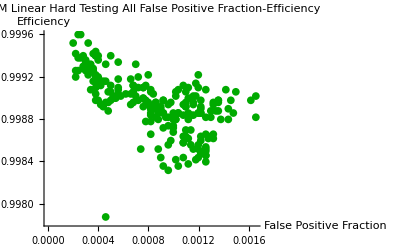

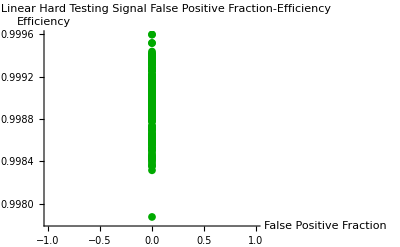

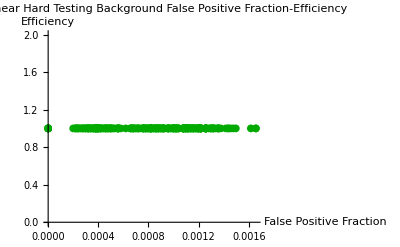

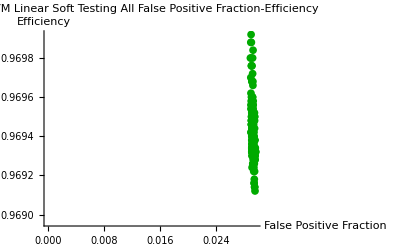

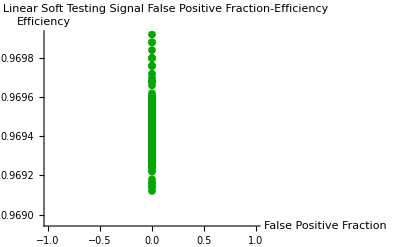

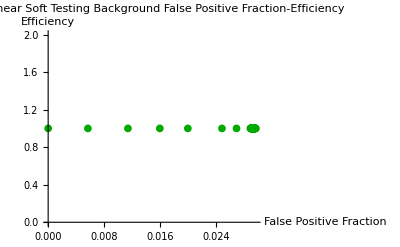

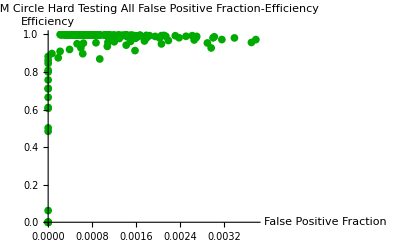

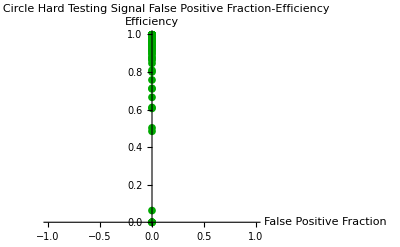

```mathematica
AllPlots[SVMFPEPlot,SVMAllRawData,SVMAllDataTypes]
```

### BDS

#### Number of Stumps-Efficiency

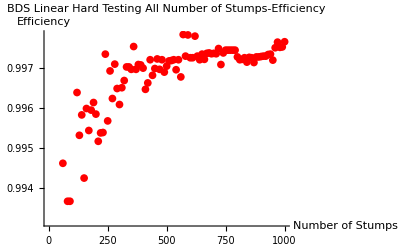

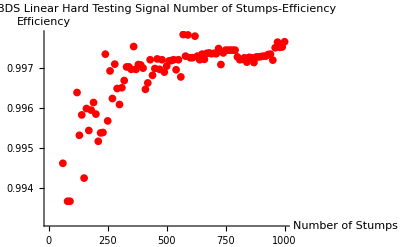

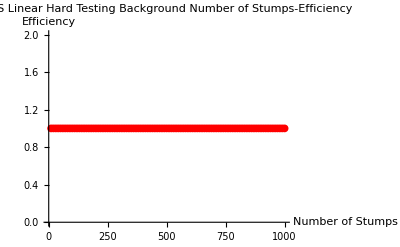

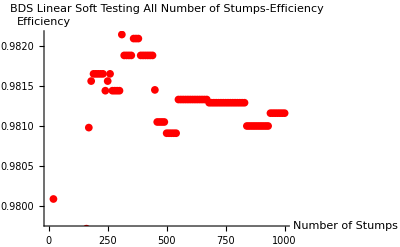

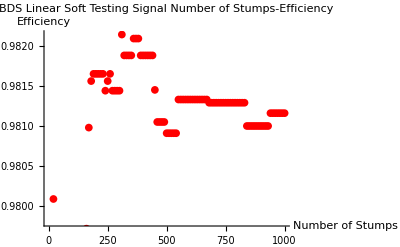

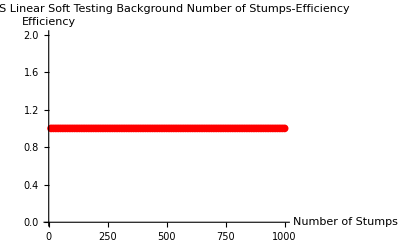

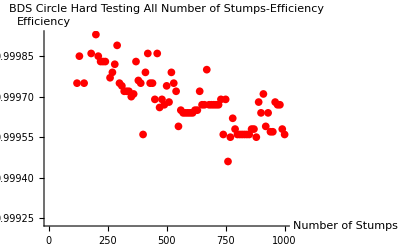

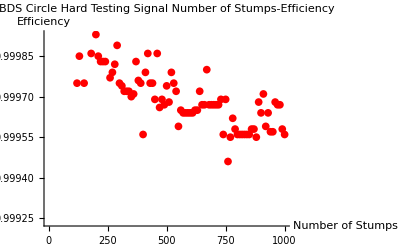

```mathematica
AllPlots[BDSSEPlot,BDSAllRawData,BDSAllDataTypes]
```

#### Number of Stumps-Distance

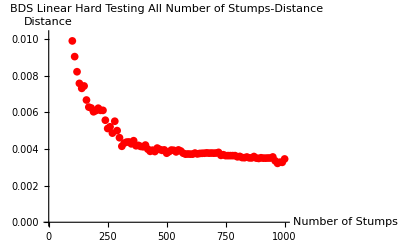

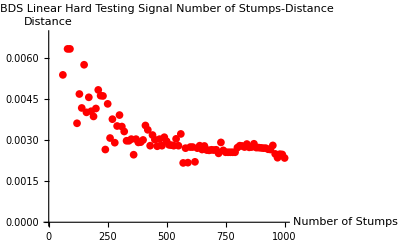

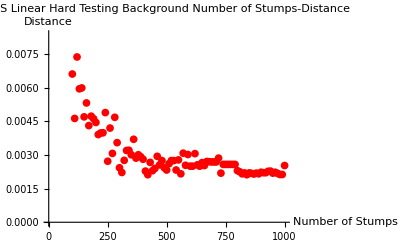

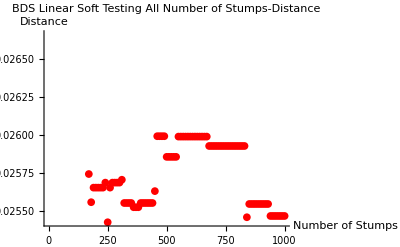

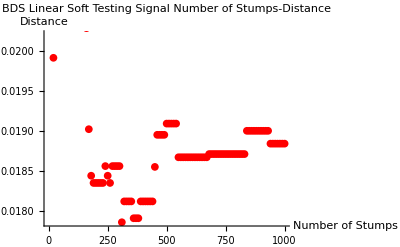

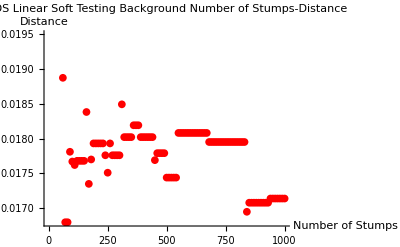

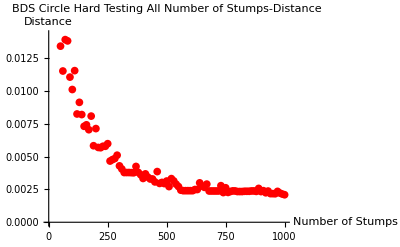

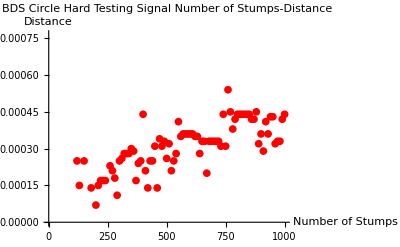

```mathematica
AllPlots[BDSSDPlot,BDSAllRawData,BDSAllDataTypes]
```

#### False Positive Fraction-Efficiency

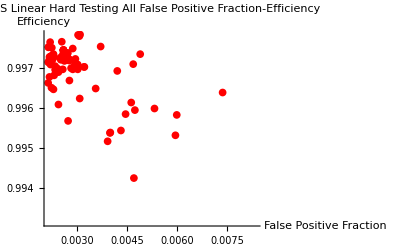

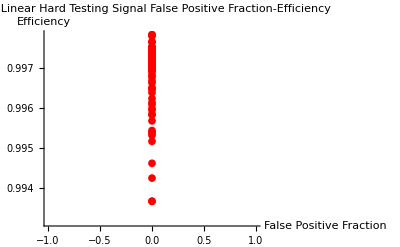

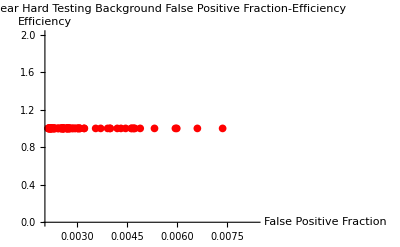

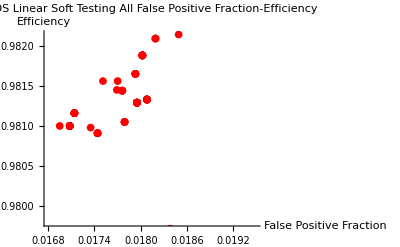

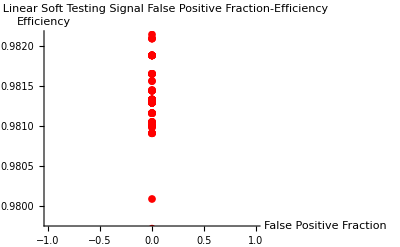

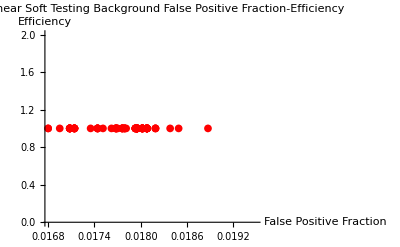

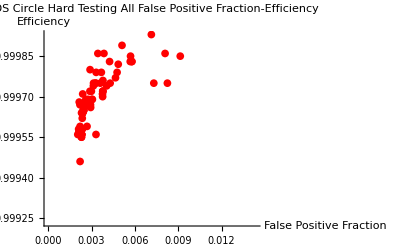

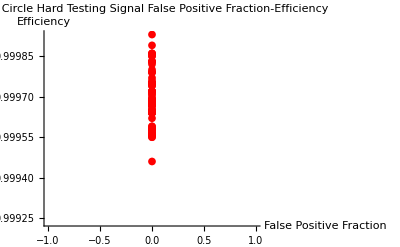

```mathematica
AllPlots[BDSFPEPlot,BDSAllRawData,BDSAllDataTypes]
```

### BDT

#### Number of Trees-Efficiency

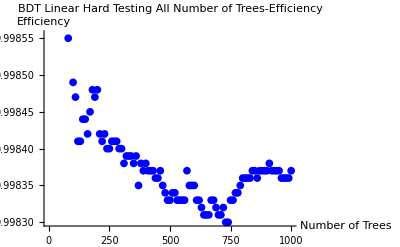

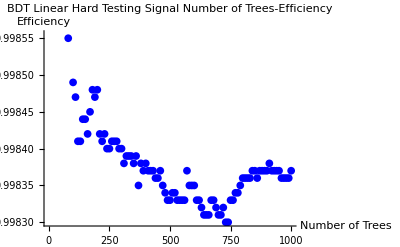

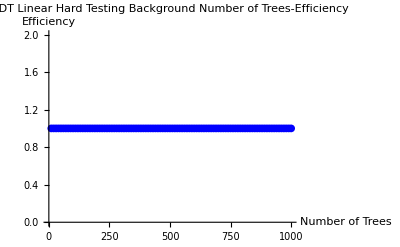

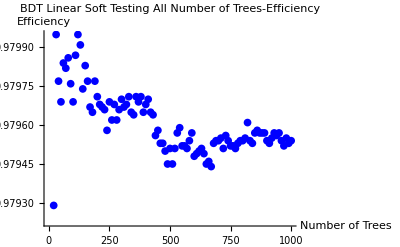

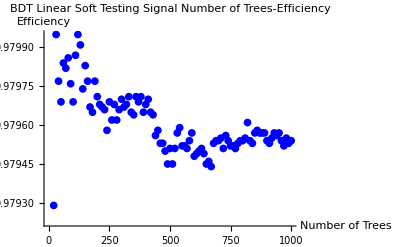

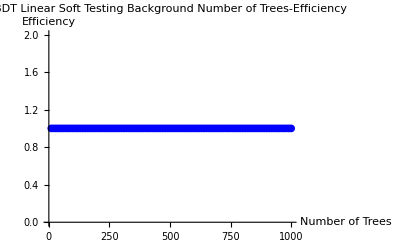

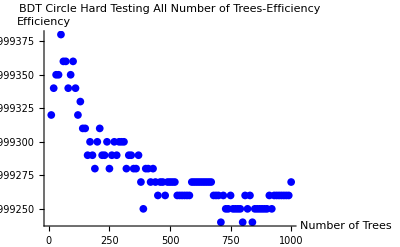

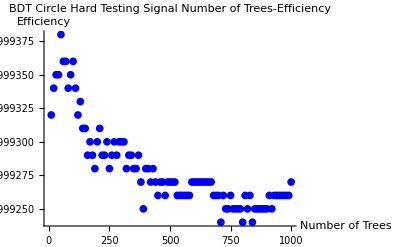

```mathematica
AllPlots[BDTTEPlot,BDTAllRawData,BDTAllDataTypes]
```

#### Number of Trees-Distance

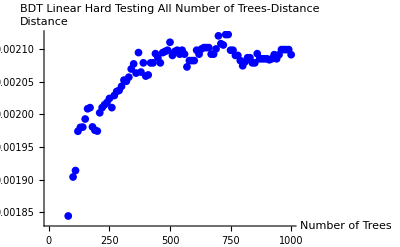

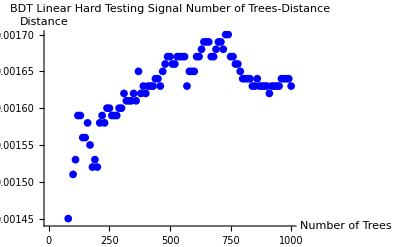

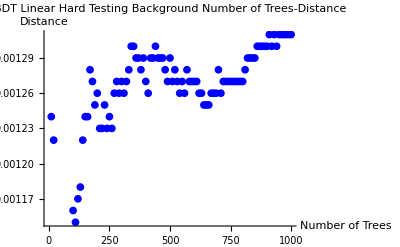

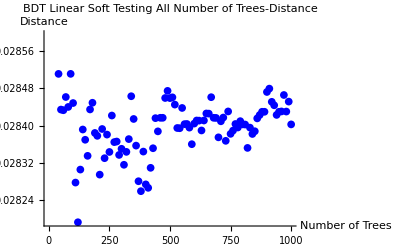

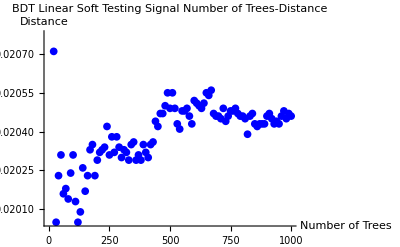

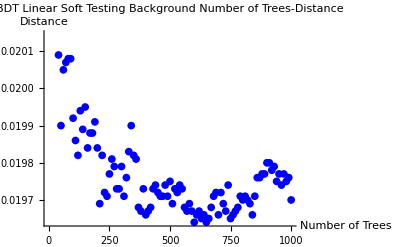

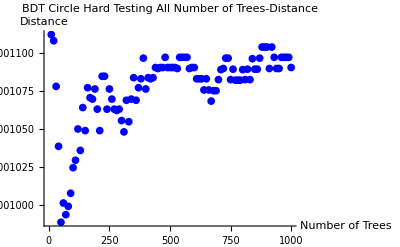

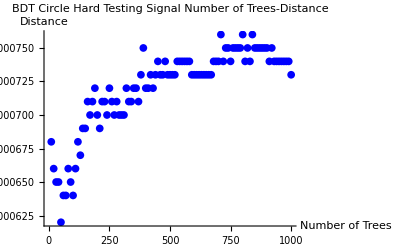

```mathematica
AllPlots[BDTTDPlot,BDTAllRawData,BDTAllDataTypes]
```

#### False Positive Fraction-Efficiency

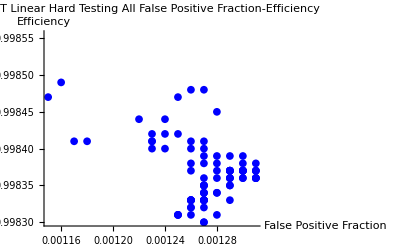

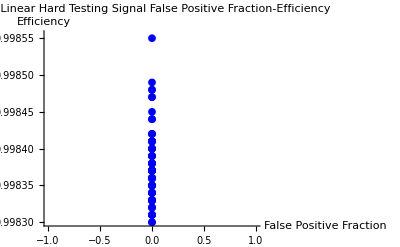

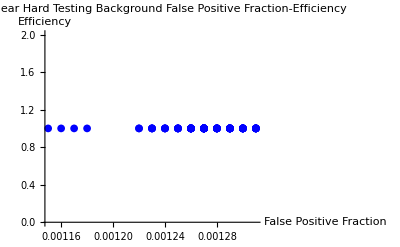

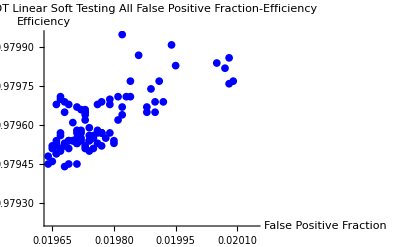

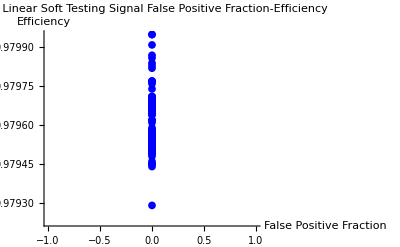

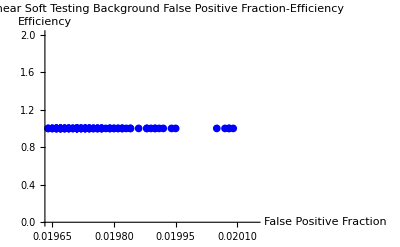

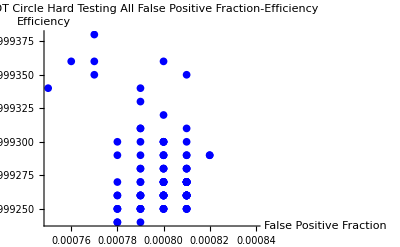

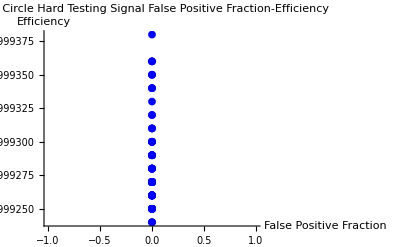

```mathematica
AllPlots[BDTFPEPlot,BDTAllRawData,BDTAllDataTypes]
```

# (*** TO DO: Finish rewriting merged plots—TRY TO GENERALIZE!!! ***)

### Merged

#### False Positive Fraction-Efficiency

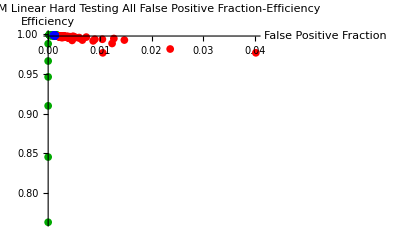

Show::gcomb: Could not combine the graphics objects in Show[SVMLinearSoftFPFNPlot, BDSLinearSoftFPFNPlot, BDTLinearSoftFPFNPlot, PlotRange → All].

Show[SVMLinearSoftFPFNPlot,BDSLinearSoftFPFNPlot,BDTLinearSoftFPFNPlot,PlotRange→All]

Show::gcomb: Could not combine the graphics objects in Show[SVMCircleHardFPFNPlot, BDSCircleHardFPFNPlot, BDTCircleHardFPFNPlot, PlotRange → All].

Show[SVMCircleHardFPFNPlot,BDSCircleHardFPFNPlot,BDTCircleHardFPFNPlot,PlotRange→All]

Show::gcomb: Could not combine the graphics objects in Show[SVMCircleSoftFPFNPlot, BDSCircleSoftFPFNPlot, BDTCircleSoftFPFNPlot, PlotRange → All].

Show[SVMCircleSoftFPFNPlot,BDSCircleSoftFPFNPlot,BDTCircleSoftFPFNPlot,PlotRange→All]

Show::gcomb: Could not combine the graphics objects in Show[SVMTwoCircleHardFPFNPlot, BDSTwoCircleHardFPFNPlot, BDTTwoCircleHardFPFNPlot, PlotRange → All].

Show[SVMTwoCircleHardFPFNPlot,BDSTwoCircleHardFPFNPlot,BDTTwoCircleHardFPFNPlot,PlotRange→All]

Show::gcomb: Could not combine the graphics objects in Show[SVMTwoCircleSoftFPFNPlot, BDSTwoCircleSoftFPFNPlot, BDTTwoCircleSoftFPFNPlot, PlotRange → All].

Show[SVMTwoCircleSoftFPFNPlot,BDSTwoCircleSoftFPFNPlot,BDTTwoCircleSoftFPFNPlot,PlotRange→All]

```mathematica
Show[SVMFPEPlot[SVMLinearHardTestingAllRawData, "Linear Hard Testing All"],BDSFPEPlot[BDSLinearHardTestingAllRawData, "Linear Hard Testing All"],BDTFPEPlot[BDTLinearHardTestingAllRawData, "Linear Hard Testing All"],PlotRange-> All]

Show[SVMLinearSoftFPFNPlot,BDSLinearSoftFPFNPlot,BDTLinearSoftFPFNPlot,PlotRange-> All]

Show[SVMCircleHardFPFNPlot,BDSCircleHardFPFNPlot,BDTCircleHardFPFNPlot,PlotRange-> All]
Show[SVMCircleSoftFPFNPlot,BDSCircleSoftFPFNPlot,BDTCircleSoftFPFNPlot,PlotRange-> All]

Show[SVMTwoCircleHardFPFNPlot,BDSTwoCircleHardFPFNPlot,BDTTwoCircleHardFPFNPlot,PlotRange-> All]
Show[SVMTwoCircleSoftFPFNPlot,BDSTwoCircleSoftFPFNPlot,BDTTwoCircleSoftFPFNPlot,PlotRange-> All]
```